# Feigenbaum Article

https://writings.stephenwolfram.com/2019/07/mitchell-feigenbaum-1944-2019-4-66920160910299067185320382/

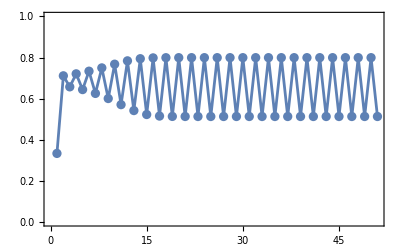

```mathematica
ListLinePlot[NestList[Compile[x,3.2 x (1-x)],N[1/3],50],Mesh->All,PlotRange->{0,1},Frame->True]
```

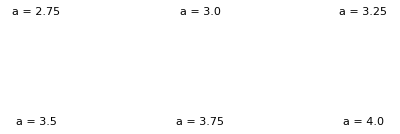

```mathematica
GraphicsGrid[Partition[Table[Labeled[ListLinePlot[NestList[Compile[x,a x (1-x)],N[1/3],50],Sequence[Mesh->All,PlotRange->{0,1},Frame->True,FrameTicks->None]],StringTemplate["a = ``"][a]],{a,2.75,4,.25}],3],Spacings->{.1,-.1}]
```

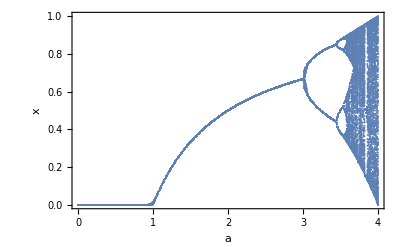

```mathematica
ListPlot[Flatten[Table[{a,#}&/@Drop[NestList[Compile[x,a x (1-x)],N[1/3],300],50],{a,0,4,.01}],1],Frame->True,FrameLabel->{"a","x"}]
```

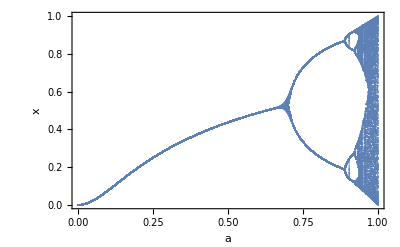

```mathematica
ListPlot[Flatten[Table[{a,#}&/@Drop[NestList[Compile[x,a Sin[Pi Sqrt@x]],N[1/3],300],50],{a,0,1,.002}],1],Frame->True,FrameLabel->{"a","x"}]
```

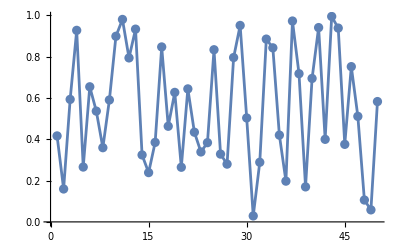

```mathematica
ListLinePlot[Rest@N[NestList[Function[x,FractionalPart[10 x]],N[Pi,100],50],40],Mesh->All]
```

```mathematica
GraphicsRow[SeedRandom[234316];
Table[ArrayPlot[CellularAutomaton[<|"RuleNumber"->294869764523995749814890097794812493824,"Colors"->4|>,3 Boole[Thread[RandomReal[{0,1},2000]<rho]],{500,{-300,300}}],FrameLabel->{None,Row[{Round[100 rho],"% black"}]}],{rho,{0.4,0.45,0.55,0.6}}],-30]
```

-Graphics-

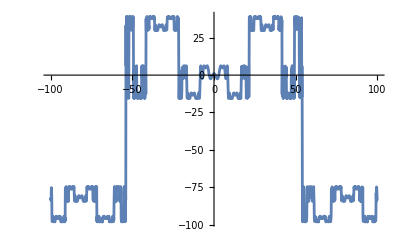

```mathematica
fUD[z_]=1.-1.5276329970363323 z^2+0.1048151947874277 z^4+0.026705670524930787 z^6-0.003527409660464297 z^8+0.00008160096594827505 z^10+0.000025285084886512315 z^12-2.5563177536625283*^-6 z^14-9.65122702290271*^-8 z^16+2.8193175723520713*^-8 z^18-2.771441260107602*^-10 z^20-3.0292086423142963*^-10 z^22+2.6739057855563045*^-11 z^24+9.838888060875235*^-13 z^26-3.5838769501333333*^-13 z^28+2.063994985307743*^-14 z^30;
fCF=Compile[{z},Module[{α=-2.5029078750959130867,n,ζ},n=If[Abs[z]<=1.,0,Ceiling[Log[-α,Abs[z]]]];
ζ=z/α^n;
Do[ζ=#,{2^n}];
α^n ζ]]&[fUD[ζ]];
Plot[fCF[x],{x,-100,100},MaxRecursion->5,PlotRange->All]
```

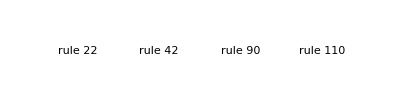

```mathematica
GraphicsRow[Labeled[ListPlot[Table[FromDigits[CellularAutomaton[#,IntegerDigits[n,2,12]],2],{n,0,2^12-1}],Sequence[AspectRatio->1,Frame->True,FrameTicks->None]],Text[StringTemplate["rule ``"][#]]]&/@{22,42,90,110}]
```

```mathematica
FractionalDigits[x_,digs_Integer]:=NestList[{Mod[2 First[#],1],Floor[2 First[#]]}&,{x,0},digs][[2;;,-1]];
GraphicsRow[Function[a,ArrayPlot[FractionalDigits[#,40]&/@NestList[a # (1-#)&,N[1/8,80],80]]]/@{2.5,3.3,3.4,3.5,3.6,4}]
```

-Graphics-